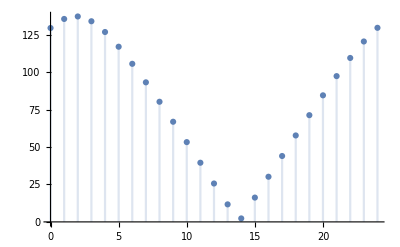

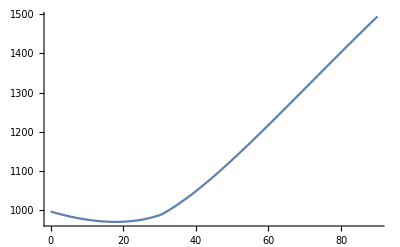

{x→17.9433}

```mathematica
f[h_,x_] := ( (* Arguments: hour of day, solar panel angle *)
sunPos = SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[{2016,7,17,h,0}]];
(* remove degree unit, then convert to radians *)
Subscript[γ, s]= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
Subscript[γ, s] = Subscript[γ, s] - Pi;
Subscript[θ, s]= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
Subscript[γ, p] = 0; (* Solar panels azimuth *)
Subscript[θ, p] = x * Pi/180; (* Solar panels angle with horizontal *)
α =ArcCos[Cos[Subscript[γ, p]-Subscript[γ, s]] Cos[Subscript[θ, s]] Sin[Subscript[θ, p]]+Cos[Subscript[θ, p]] Sin[Subscript[θ, s]]]*180/Pi
)
(* Plot angle to sun for solar panels at 30 degrees *)
DiscretePlot[f[x,30],{x,0,24}]
(* Define a function that sums up the total of angles to the sun *)
position = GeoPosition[{51.546545,4.411744}];
sunUp = Sunrise[position];
sunUpHour = DateValue[sunUp,"Hour"]+DateValue[sunUp, "Minute"]/60;
sunset = Sunset[position];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
g[x_]=Sum[f[h,x],{h,sunUpHour,sunsetHour}];
(* Find for which angle of the solar panels this value is minimal *)
Plot[g[x],{x,0,90}]
FindMinimum[g[x],{x,0,0,24}][[2]]
```